#### Preamble

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_ISA.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/jet_jet-extended.wls"

fs = 9;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
graphsOpts:= {Mesh-> Full,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> ColorData[3]}
SetOptions[ListLinePlot,graphsOpts];
```

/home/juanathan/Documentos/Wolfram Mathematica/Wolfram_scripts

```mathematica
jet[u_?NumericQ] := 
 Blend[{{0, RGBColor[0, 0, 9/16]}, {1/9, Blue}, {23/63, Cyan}, {13/21,
      Yellow}, {47/63, Orange}, {55/63, Red}, {1, 
     RGBColor[1/2, 0, 0]}}, u] /; 0 <= u <= 1
myGraytones[u_?NumericQ] := 
 Blend[{{0, GrayLevel[0.0]}, {0.2, GrayLevel[0.4]}, {0.4, 
     GrayLevel[0.6]}, {1, GrayLevel[1]}}, u] /; 0 <= u <= 1
prueba3[limite_, max_] := 
  If[#1 <= limite, (myGraytones[#] &[
      Rescale[#1, {0, limite}]]), (jet[#] &[
      Rescale[#1, {limite, max}]])] &;
      
BarLegend[{prueba3[0.1, lim1], {0, lim1}}, LegendLayout -> "Row", 
 LabelStyle -> 
  Directive[Black, FontSize -> 15, FontFamily -> "Times"]]
```

BarLegend[{If[#1≤0.1,(myGraytones[#1]&)[Rescale[#1,{0,0.1}]],(jet[#1]&)[Rescale[#1,{0.1,lim1}]]]&,{0,lim1}},LegendLayout→Row,LabelStyle→Directive[GrayLevel[0],FontSize→15,FontFamily→Times]]

#### Common Parameters

```mathematica
ang = Range[0,90,1.]*Pi/180.;
lda = {550., 600., 650};

rad = 60.;
mu  = 60.;(*Central value of the Radii Distribution*)
cfrac = .20;

(*To recover fresnel*)
ind = Transpose[{1.,1.,1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
(*Au NPs with no size correction*)
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
indAu = Transpose[{1.,3.5,1.5}&/@ lda];
ind1 = Transpose[{1., 1.} & /@ lda];
ind2 = Transpose[{1., 1.5} & /@ lda];
```

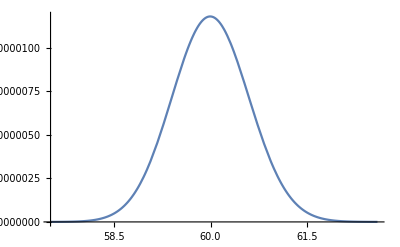

(cfrac Exp[-2 Log[#3]^2] Exp[-(Log[#1/#2]/(√2. Log[#3]))^2])/((π #2^2) (#1 √(2. π) Log[#3]))&

```mathematica
sigma =1.01;(*Standard deviation from Raddii Distribution*)

(*Upper and lower integration limits fo the polydispersed case*)
sizeDist = cfrac * Exp[-2*Log[#3]^2]/(Pi * #2^2) * Exp[-(Log[#/#2]/(Sqrt[2.]*Log[#3]))^2] / (#*Sqrt[2.*Pi]*Log[#3])&;
Plot[sizeDist[x,mu,sigma],{x,mu*sigma^(-Sqrt[18.]),mu*sigma^(Sqrt[18.])},PlotRange->All]
sizeDist
```

### Fresnel

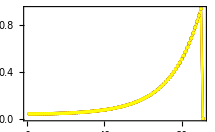
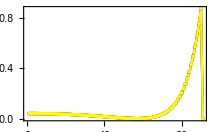
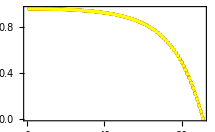
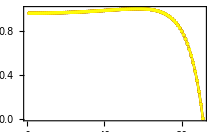

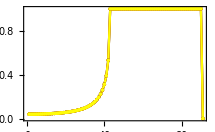
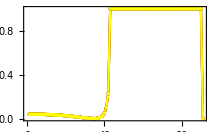
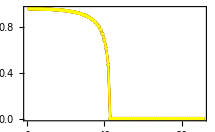
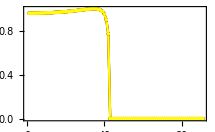

```mathematica
fresnel = Through[{fresnelRs, fresnelRp,fresnelTs,fresnelTp}[ang, toMap/@ind2]]; (*[[rt*pol, ang, lda*)
imp1 = CSMImpedance[ang,#]&/@{ind1, ind1, ind2, ind2};
fresnel= Transpose[fresnel,2<->3];
imp1 = Transpose[imp1, 2<->3];
frext = ListLinePlot[#,PlotRange->All]&/@(imp1*norm2[fresnel])

fresnel = Through[{fresnelRs, fresnelRp,fresnelTs,fresnelTp}[ang, toMap/@ Reverse@ind2]]; (*[[rt*pol, ang, lda*)
imp2 = CSMImpedance[ang,#]&/@{ind1, ind1,  Reverse@ind2,  Reverse@ind2};
fresnel= Transpose[fresnel,2<->3];
imp2 = Transpose[imp2, 2<->3];
frint = ListLinePlot[#,PlotRange->All]&/@(imp2*norm2[fresnel])
```

## Monodisperse (Recovering Fresnel)

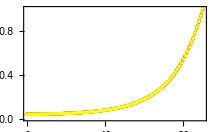
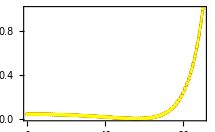

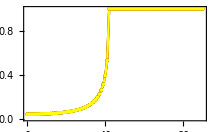
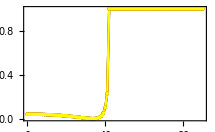

```mathematica
CSM3MediaReflectionExt[ang, ind, lda, rad, cfrac] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSM3MediaReflectionInt[ang, ind, lda, 50., .1];
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %
```

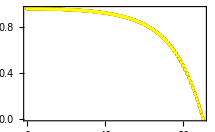
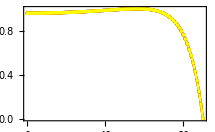

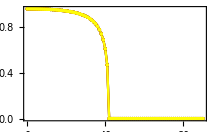
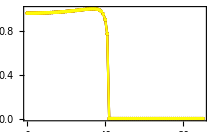

```mathematica
CSM3MediaTransmissionExt[ang, ind, lda, rad, cfrac];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSM3MediaTransmissionInt[ang, ind, lda, 50., .1];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])
```

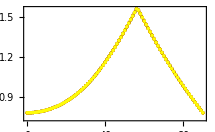
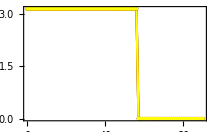

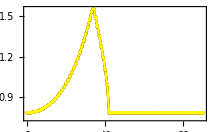
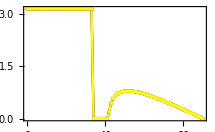

```mathematica
CSM3MediaElipsometryExt[ang, ind, lda, rad, cfrac] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSM3MediaElipsometryInt[ang, ind, lda, rad, cfrac];
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %
```

## Polydisperse (Recovering Fresnel)

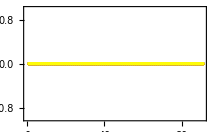
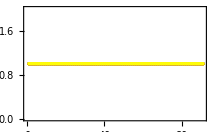

{-Graphics-,-Graphics-}

```mathematica
(*CSMPolyAmplitudeReflectionTransmission = {{rs,ts},{rp,tp}}*)
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM.wls"
data = CSMPolyAmplitudeReflectionTransmission[ang, ind1,lda, cfrac, {mu, sigma, sizeDist}];
ListLinePlot[norm2[#]]&/@Transpose[data[[1]] ,2<->3]
ListLinePlot[norm2[#]]&/@Transpose[data[[2]] ,2<->3]
```

```mathematica
CSMPolyReflectionExt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyReflectionInt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
CSMPolyTransmissionExt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSMPolyTransmissionInt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
CSMPolyElipsometryExt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyElipsometryInt[ang, ind, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

## Mono vs Polydisperse (Gold AuNP)

```mathematica
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
indAu = Transpose[{1.,3.5,1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
```

```mathematica
indAu
```

{{1.,1.,1.},{3.5,3.5,3.5},{1.5,1.5,1.5}}

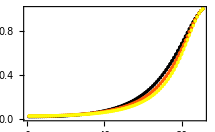
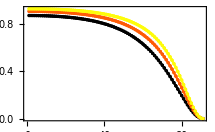

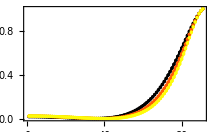
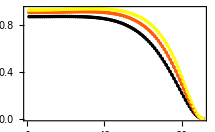

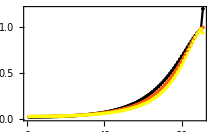
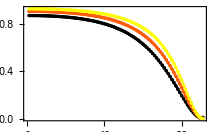

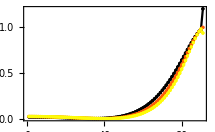
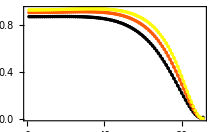

```mathematica
dataMono = CSMAmplitudeReflectionTransmission[ang, indAu[[;;2]],lda, rad,cfrac];
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataMono[[1]] ,2<->3]
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataMono[[2]] ,2<->3]

dataPoly = CSMPolyAmplitudeReflectionTransmission[ang, indAu[[;;2]],lda, cfrac, {mu, sigma, sizeDist}];
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataPoly[[1]] ,2<->3]
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataPoly[[2]] ,2<->3]
```

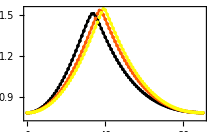
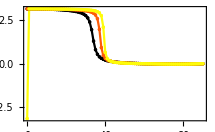

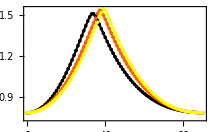
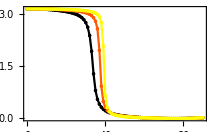

```mathematica
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]&/@ ({ArcTan[Abs[#]],Arg[#]}&@ (Divide@@dataMono[[;;,1]]))
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]&/@ ({ArcTan[Abs[#]],Arg[#]}&@ (Divide@@dataPoly[[;;,1]]))
```

```mathematica
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
```

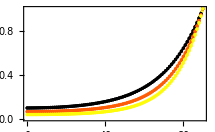
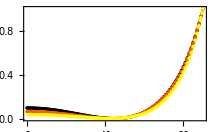

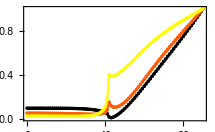
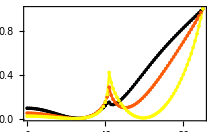

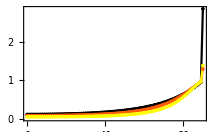
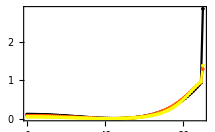

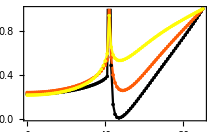
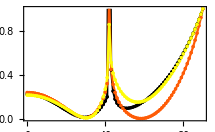

```mathematica
CSM3MediaReflectionExt[ang, indAu, lda, rad, cfrac] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSM3MediaReflectionInt[ang, indAu, lda, rad, cfrac];
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyReflectionExt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyReflectionInt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->{0,1}]& /@ %
```

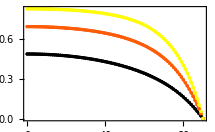
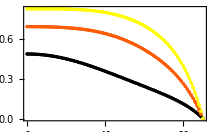

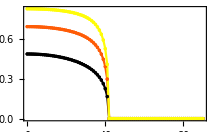
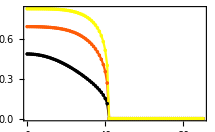

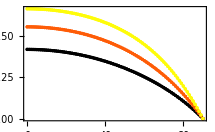
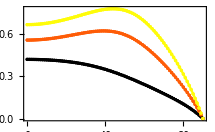

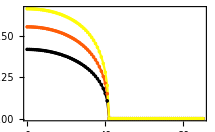
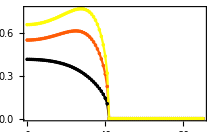

```mathematica
CSM3MediaTransmissionExt[ang, indAu, lda, rad, cfrac];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSM3MediaTransmissionInt[ang, indAu, lda, rad, cfrac];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])

CSMPolyTransmissionExt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSMPolyTransmissionInt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])
```

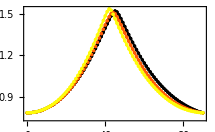
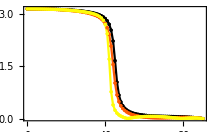

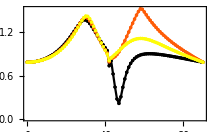
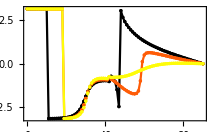

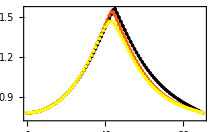
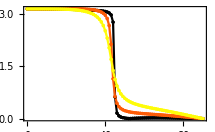

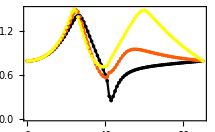
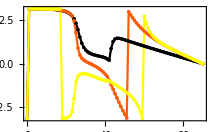

```mathematica
CSMPolyElipsometryExt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %
CSMPolyElipsometryInt[ang, indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSM3MediaElipsometryExt[ang, indAu, lda, rad, cfrac] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %
CSM3MediaElipsometryInt[ang, indAu, lda, rad, cfrac];
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %
```

## Algo acá

```mathematica
ang = Range[0,60,2]*Pi/180.;
lda = Range[400,750,2.5];

ind = Transpose[{1.,1.,1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
(*Au NPs with no size correction*)
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
indAu = Transpose[{1.,3.5,1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
sizeDist
```

(cfrac Exp[-2 Log[#3]^2] Exp[-(Log[#1/#2]/(√2. Log[#3]))^2])/((π #2^2) (#1 √(2. π) Log[#3]))&

```mathematica
dataPoly=CSMPolyReflectionExt[ang,indAu, lda, cfrac,{mu, sigma, sizeDist}] ;
dataMono=CSM3MediaReflectionExt[ang, indAu, lda, mu, cfrac];
```

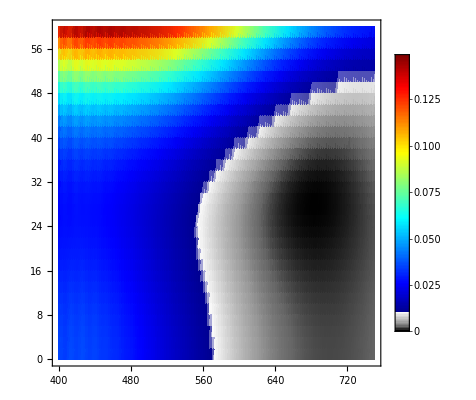
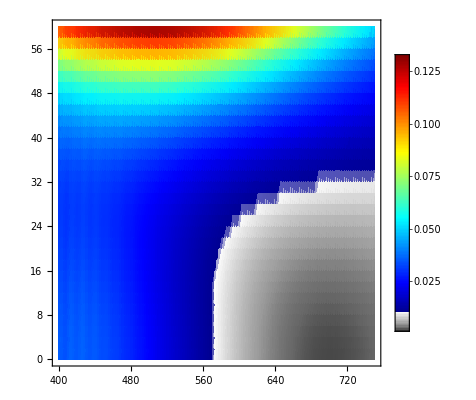

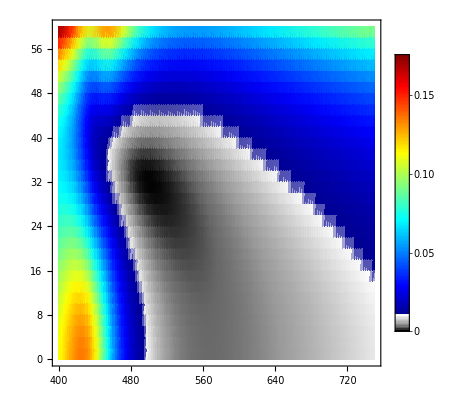
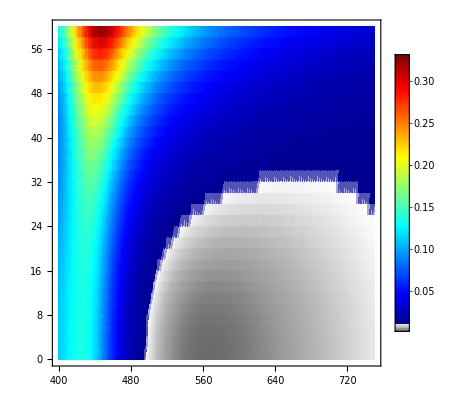

```mathematica
ListDensityPlot[norm2[#],DataRange->{{400,750},{0,60}},ColorFunctionScaling->False,ColorFunction->prueba3[0.01,Max[norm2[#]]],PlotRange->Full,PlotLegends->Automatic]& /@dataPoly
ListDensityPlot[norm2[#],DataRange->{{400,750},{0,60}},ColorFunctionScaling->False,ColorFunction->prueba3[0.01,Max[norm2[#]]],PlotRange->Full,PlotLegends->Automatic]& /@dataMono
```

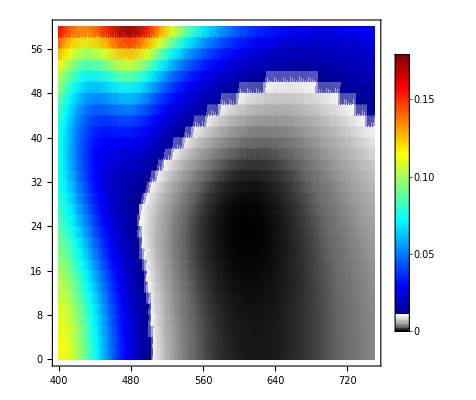
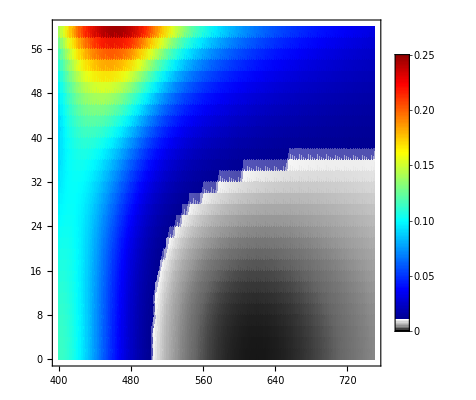

{-Graphics-,-Graphics-}

```mathematica
ListDensityPlot[norm2[#],DataRange->{{400,750},{0,60}},ColorFunctionScaling->False,ColorFunction->prueba3[0.01,Max[norm2[#]]],PlotRange->Full,PlotLegends->Automatic]& /@dataPoly
ListDensityPlot[norm2[#],DataRange->{{400,750},{0,60}},ColorFunctionScaling->False,ColorFunction->prueba3[0.01,Max[norm2[#]]],PlotRange->Full,PlotLegends->Automatic]& /@dataMono
```

Ceiling[#1+4. #1^(1./3)+2.]&

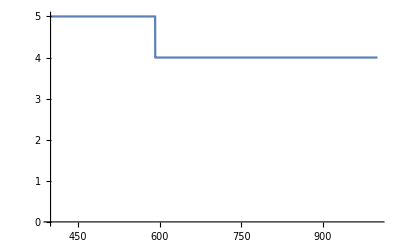
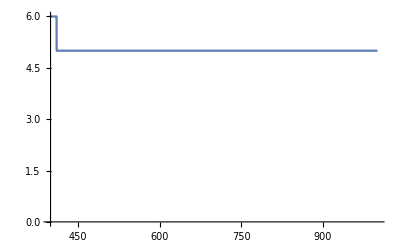
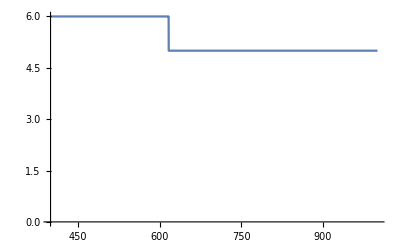
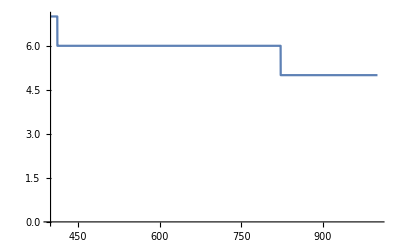
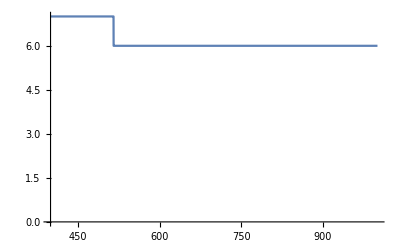
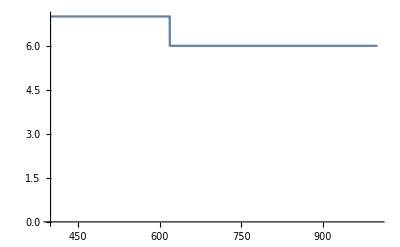

```mathematica
wacombe = Ceiling[# + 4.*#^(1./3) + 2.]&
Plot[wacombe[2π*#/lda],{lda,400,1000},PlotRange->{0,Automatic}]&/@Range[10,60,10]
```

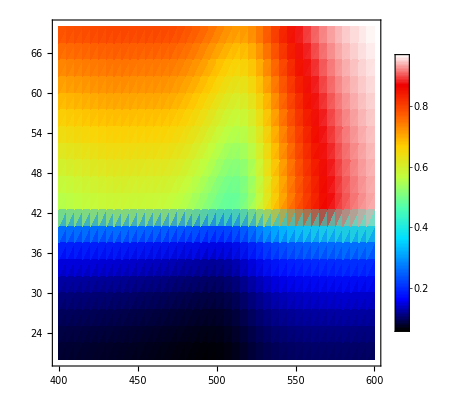
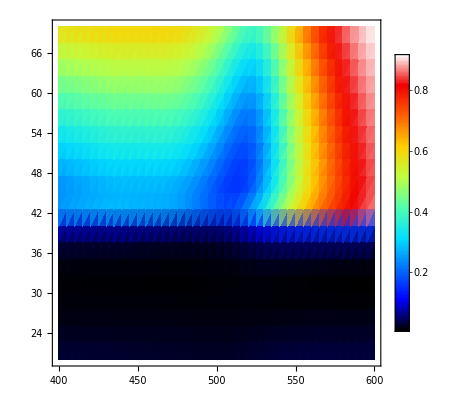

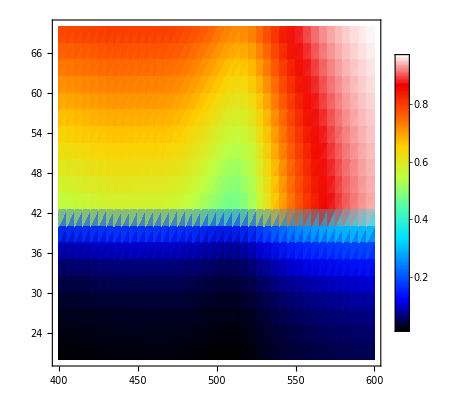
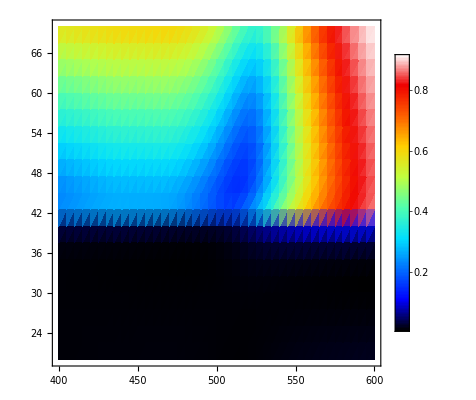

```mathematica
ListDensityPlot[norm2[#],DataRange->{{400,600},{20,70}},ColorFunction->JetExtended,PlotRange->Full,PlotLegends->Automatic]& /@dataPoly
ListDensityPlot[norm2[#],DataRange->{{400,600},{20,70}},ColorFunction->JetExtended,PlotRange->Full,PlotLegends->Automatic]& /@dataMono
```